# Practical-2

Akshay Kumar (204005)
NA Practicals

### Newton Method

#### Ques-1. Find the root of the function f[x]=Cos[x] with maximum number of iteration is 5.

The final approximation of the root for iteration 1 : 1.64209

The final approximation of the root for iteration 2 : 1.57068

The final approximation of the root for iteration 3 : 1.5708

The final approximation of the root for iteration 4 : 1.5708

The final approximation of the root for iteration 5 : 1.5708

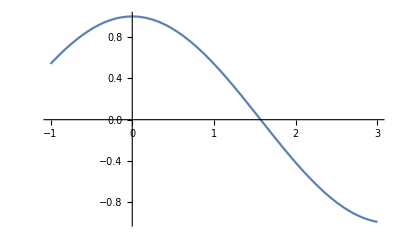

```mathematica
x0=1;
NMax=5;
f[x_]:=Cos[x];
For[i=1,i<=NMax,i++,
x1=N[x0-(f[x0])/(f'[x0])];
x0=x1;
Print["The final approximation of the root for iteration ",i," : ",x1]];
Plot[f[x],{x,-1,3}]
```

### Ques-2. f(x)=x^3+x^2-3x-3, (1,2)

The final approximation of the root for iteration 1 : 3.

The final approximation of the root for iteration 2 : 2.2

The final approximation of the root for iteration 3 : 1.83015

The final approximation of the root for iteration 4 : 1.7378

The final approximation of the root for iteration 5 : 1.73207

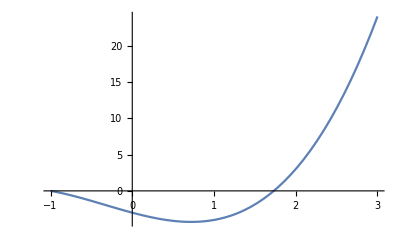

```mathematica
x0=1;
NMax=5;
f[x_]:=x^3+x^2-3x-3;
For[i=1,i<=NMax,i++,
x1=N[x0-(f[x0])/(f'[x0])];
x0=x1;
Print["The final approximation of the root for iteration ",i," : ",x1]];
Plot[f[x],{x,-1,3}]
```

### Ques-3. f(x)=Sinx, (3,4)

The final approximation of the root for iteration 1 : 3.14255

The final approximation of the root for iteration 2 : 3.14159

The final approximation of the root for iteration 3 : 3.14159

The final approximation of the root for iteration 4 : 3.14159

The final approximation of the root for iteration 5 : 3.14159

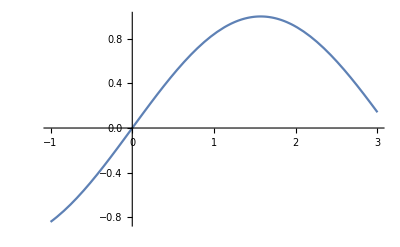

```mathematica
x0=3;
NMax=5;
f[x_]:=Sin[x];
For[i=1,i<=NMax,i++,
x1=N[x0-(f[x0])/(f'[x0])];
x0=x1;
Print["The final approximation of the root for iteration ",i," : ",x1]];
Plot[f[x],{x,-1,3}]
```

### Ques-4. f(x)=1-logx, (2,3)

The final approximation of the root for iteration 1 : 2.61371

The final approximation of the root for iteration 2 : 2.71624

The final approximation of the root for iteration 3 : 2.71828

The final approximation of the root for iteration 4 : 2.71828

The final approximation of the root for iteration 5 : 2.71828

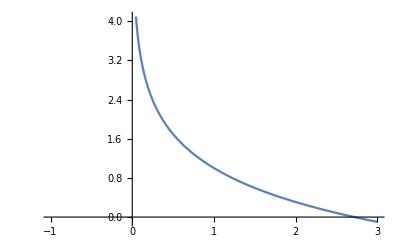

```mathematica
x0=2;
NMax=5;
f[x_]:=1-Log[x];
For[i=1,i<=NMax,i++,
x1=N[x0-(f[x0])/(f'[x0])];
x0=x1;
Print["The final approximation of the root for iteration ",i," : ",x1]];
Plot[f[x],{x,-1,3}]
```

### Ques-5. f(x)=x^2-5, (2,3)

The final approximation of the root for iteration 1 : 2.25

The final approximation of the root for iteration 2 : 2.23611

The final approximation of the root for iteration 3 : 2.23607

The final approximation of the root for iteration 4 : 2.23607

The final approximation of the root for iteration 5 : 2.23607

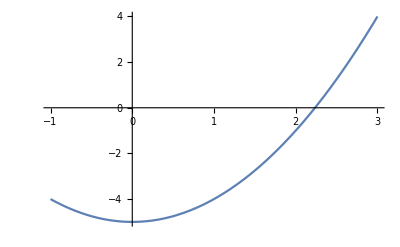

```mathematica
x0=2;
NMax=5;
f[x_]:=x^2-5;
For[i=1,i<=NMax,i++,
x1=N[x0-(f[x0])/(f'[x0])];
x0=x1;
Print["The final approximation of the root for iteration ",i," : ",x1]];
Plot[f[x],{x,-1,3}]
```